Training of the data:

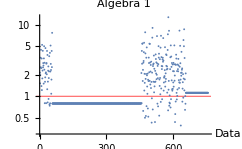
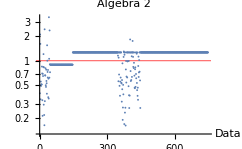
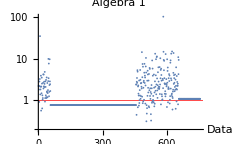
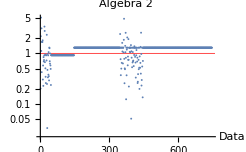
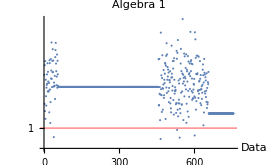
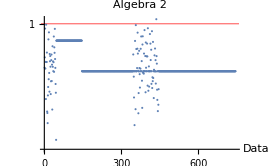
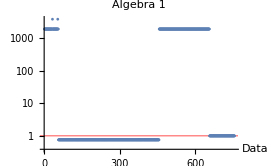
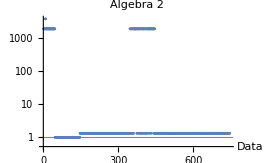
Method | Algebra1  | Algebra 2 | Accuracy
Automatic | -Graphics- | -Graphics- | 0.58
Neural Network | -Graphics- | -Graphics- | 0.59
Logistic Regression | -Graphics- | -Graphics- | 0.50
Naive Bayesian | -Graphics- | -Graphics- | 0.67
Nearest Neighbor | -Graphics- | -Graphics- | 0.57
Gradiant Boosted Trees | -Graphics- | -Graphics- | 0.59
Markov | -Graphics- | -Graphics- | 0.93
Support Vector Machine | -Graphics- | -Graphics- | 0.57
Random Forest | -Graphics- | -Graphics- | 0.63
Decision Tree | -Graphics- | -Graphics- | 0.50

Contextual Tags

Value | Meaning
0 | No Context Restrictions
1 | Simplest Form Fraction
2 | Decimal Representation
3 | A set of Points
4 | Calculus
5 | A set of Points of Simplest Fractions
6 | A set of Points in Decimal
7 | Mixed Number
8 | Improper Fraction

Package
correctAnswer[answer_, correct_]:=MatchQ[Interpreter["MathExpression"][answer], Interpreter["MathExpression"][correct]]
turnOffEquivFrac[question_]:=StringMatchQ[question, {"*raction*implest form"}];
isMatrix[answer_]:=MatchQ[answer, MatrixForm];
allpoints[question_]:=StringMatchQ[question, {"*all points*"}];
eitherPointfirst[a_, b_,c_, d_]:= {{"(",a, b, ")"},{"("c, d ")"}}-> {{"("c, d ")"},{"(",a, b, ")"}}
isPoint[answer_]:=StringMatchQ[answer, {"(*,*)"}];
improperFraction[question_]:=StringMatchQ[question, "*mproper fraction*"];
decForm[question_]:=StringMatchQ[question, "*ecimal form*"];
isCalc[question_]:=StringMatchQ[question, {"*erivative*", "*ifferniate*", "*ntegra*", "*aylor*xpand*", "*acLa*xpand*", "*imit*"}];
mixedNumber[question_]:=StringMatchQ[question, "*ixed number*"];
(*This is the wrong way to do it, patern matching is better here*)
expandToSix[answer_, correct_, x_]:=If[Series[answer, {x, 0, 6}]==Series[correct, {x, 0, 6}], True, False]
algebratheorems={ForAll[{a,b,c}, g[a, g[b,c]]==g[g[a, b], c]], 
				 ForAll[{a,b}, g[a, b]==g[b,a]], 
				 ForAll[{a,b}, f[a,b]==f[b,a]],
				 ForAll[{a,b,c}, f[a,f[b,c]]==f[f[a,b],c]],
				 ForAll[{a,b,c}, f[a, g[c,b]]==g[f[a,c], f[a,b]]],
				 ForAll[a, g[a,e]==a],
				 ForAll[a, f[a, e]==e],
				 ForAll[a, f[a, n]==a],
				 ForAll[a, g[a, inv[a]]==e],
				 ForAll[a, f[a, inv1[a]]==n]} (*This defines an abelian ring w/ distributive property*)
				 
algebraandtrigtheorems={ForAll[{a,b,c}, g[a, g[b,c]]==g[g[a, b], c]], 
				 ForAll[{a,b}, g[a, b]==g[b,a]], 
				 ForAll[{a,b}, f[a,b]==f[b,a]],
				 ForAll[{a,b,c}, f[a,f[b,c]]==f[f[a,b],c]],
				 ForAll[{a,b,c}, f[a, g[c,b]]==g[f[a,c], f[a,b]]],
				 ForAll[a, g[a,e]==a],
				 ForAll[a, f[a, e]==e],
				 ForAll[a, f[a, n]==a],
				 ForAll[a, g[a, inv[a]]==e],
				 ForAll[a, f[a, inv1[a]]==n], 
				 ForAll[{a,b}, sin[g[a,b]]==g[f[sin[a],cos[b]], f[sin[b], cos[a]]]],
				 ForAll[ {a,b}, cos[g[a,b]]==g[f[cos[a],cos[b]], f[sin[inv[b]], sin[a]]]],
				 ForAll[a, sin[inv[a]]==inv[sin[a]]],
				 ForAll[a, cos[inv[a]]==cos[a]],
				 ForAll[a, g[f[sin[a],sin[a]], f[cos[a], cos[a]]]==n]}
theorems=<|"algebra 1"-> {algebratheorems}, "algebra 2"-> {algebraandtrigtheorems}, "calc"-> {algebraandtrigtheorems}|>;
removeSinCos[given_]:=given/.{Sin->sin, Cos->cos} 
removeSinCos[Sin[5]+Cos[x]]
replacePlus[given_]:=given/.{Plus-> g, Times[-1, amin_]->inv[amin]}
replacePlus[a-b]
replaceMulti[given_]:=given/.{Times-> f, Power[adiv_, -1]-> inv1[adiv]}
replaceTanSecCscCot[given_]:=given/.{Tan[atan_]-> f[sin[atan],inv1[cos[atan]]], Sec[asec_]-> inv1[cos[asec]], Csc[acsc_]-> inv1[sin[acsc]], Cot[acot_]-> f[inv1[sin[acot]],cos[acot]]}
replaceTanSecCscCot[Tan[y]+ Csc[x]]
removeProperFormat[given_]:=replacePlus[replaceMulti[removeSinCos[replaceTanSecCscCot[given]]]]
determinetags[question_]:=If[allpoints[question], 
									If[turnOffEquivFrac[question], 5, 
												If[decForm[question], 6, 3]],
									If[turnOffEquivFrac[question], 1, 
											If[decForm[question], 2, 
												If[isCalc[question], 4, 
													If[mixedNumber[question], 7, 
														If[improperFraction[question], 8, 0]
													   ]
													]
												]
											]
								]; 


equivalentAnswer[level_, tags_, answer_, correct_]:=
Module[{formattedanswer, formattedcorrectanswer, proof}, 
			
				If[tags==4, level="calc"];
				Switch[tags, 
				0| 3| 4, If[correctAnswer[answer, correct], True, If[Simplify[Interpreter["MathExpression"][answer]- Interpreter["MathExpression"][correct]]==0, 
					If[UnsameQ[Head[Interpreter["MathExpression"][answer]], Failure], 
						formattedanswer:=removeProperFormat[Interpreter["MathExpression"][answer]];
						formattedcorrectanswer=removeProperFormat[Interpreter["MathExpression"][correct]];
						proof=TimeConstrained[FindEquationalProof[formattedanswer==formattedcorrectanswer , theorems[level]],10];
							If[proof["Logic"]=="EquationalLogic", 
								If[Complement[Query[Key[{"SubstitutionLemma", All}proof["ProofDataset"]["Statement"]]], theorems[level]]=={}, True, False],
								False],
						False],
					False]],
				1, If[correctAnswer[answer, correct], True, False], 
				2, If[correctAnswer[answer, correct], True, False], 
				5, If[Complement[StringSplit[answer, "),("], StringSplit[correct, "),("]]=={}, True, False],  
				6, If[Complement[StringSplit[answer, "),("], StringSplit[correct, "),("]]=={}, True, False],
				_, MatchQ[answer, correct] (*exact match is default case*)
				
				]] 
				
checkforEquivlentanswers[question_, answer_, correct_, level_]:=
Module[{t},
			t=determinetags[question];
			equivalentAnswer[level, t, answer, correct]]	
equivalentAnswer["algebra 1", 7, "1 1/4", "5/4"]